Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики

ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №1

 Обобщенные функции
 
Вариант №2

Выполнил: студент группы 0В01
Белясов Архип
Проверил: Богданов О.В.

Задание 1
	Найти отклонение струны под действием сосредоточенных сил,
представить решение графически (см. пример 1). Произвольно изменить
значения сосредоточенных нагрузок. Сделать выводы. Если: 
L=18, сосредоточенные нагрузки flist=[1,-1,3,-3] приложены в точках x_i=1, 2, 3, 4.

```mathematica
Clear[L,xx,X,ff,f,ds,k]
```

```mathematica
L =18;
xx= {1, 2, 3, 4};
ff = {1, -1, 3, -3};
```

```mathematica
xx=xx*(L-1)/4;
```

```mathematica
fun=0;
```

```mathematica
For[i=1, i<=Length[xx],i++, fun=fun+ ff[[i]]*DiracDelta[x-xx[[i]]]]
```

```mathematica
fun
```

3 DiracDelta[-17+x]+2 DiracDelta[-17+2 x]-12 DiracDelta[-51+4 x]-4 DiracDelta[-17+4 x]

```mathematica
f[x_]= fun;
```

```mathematica
ds = DSolve[{ u''[x]==f[x], u[0]==0,u[L] == 0},u[x],x];
```

```mathematica
z[x_]= Simplify[ds[[1,1,2,2]]];
```

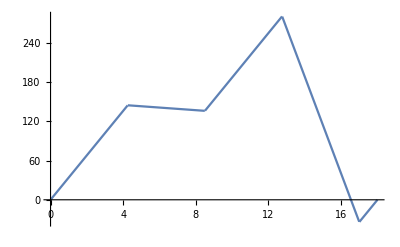

```mathematica
Plot[z[x],{x,0,L}]
```

Изменим знаки сосредоточенных нагрузок на противоположные:

```mathematica
L =18;
xx= {1, 2, 3, 4};
ff = {1,-1, 3, -3};
```

```mathematica
xx=xx*(L-1)/4;
```

```mathematica
fun=0;
```

```mathematica
For[i=1, i<=Length[xx],i++, fun=fun+ ff[[i]]*DiracDelta[x-xx[[i]]]]
```

```mathematica
fun
```

-3 DiracDelta[-17+x]-2 DiracDelta[-17+2 x]+12 DiracDelta[-51+4 x]+4 DiracDelta[-17+4 x]

```mathematica
f[x_]= fun;
```

```mathematica
ds = DSolve[{ u''[x]==f[x], u[0]==0,u[L] == 0},u[x],x];
```

```mathematica
g[x_]= Simplify[ds[[1,1,2,2]]];
```

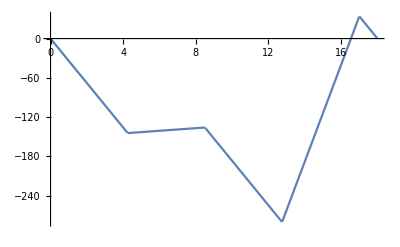

```mathematica
Plot[g[x],{x,0,L}]
```

Возьмем сосредоточенные нагрузки по модулю:

```mathematica
L =18;
xx= {1, 2, 3, 4};
ff = {1,1, 3, 3};
```

```mathematica
xx=xx*(L-1)/4;
```

```mathematica
fun=0;
```

```mathematica
For[i=1, i<=Length[xx],i++, fun=fun+ ff[[i]]*DiracDelta[x-xx[[i]]]]
```

```mathematica
fun
```

3 DiracDelta[-17+x]+2 DiracDelta[-17+2 x]+12 DiracDelta[-51+4 x]+4 DiracDelta[-17+4 x]

```mathematica
f[x_]= fun;
```

```mathematica
ds = DSolve[{ u''[x]==f[x], u[0]==0,u[L] == 0},u[x],x];
```

```mathematica
g[x_]= Simplify[ds[[1,1,2,2]]];
```

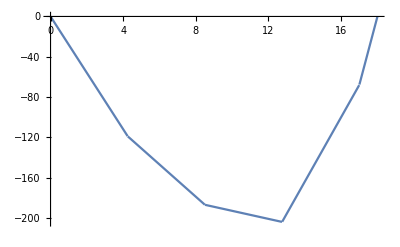

```mathematica
Plot[g[x],{x,0,L}]
```

Вывод:
	Найдено отклонение струны под действием сосредоточенных сил. При изменении знаков сосредоточенных нагрузок на противоположные прогиб струны меняется. Если взять сосредоточенные нагрузки по модуль, то прогиб струны меняется и график становится более гладким.

Задание 2
	В среде Wolfram Mathematica найти свертку обобщенных функций и
придумать 2 примера, где операция сверки обобщенных функций не
определена, обосновать в выводе свой выбор : θ(x) * θ(x)

```mathematica
Convolve[HeavisideTheta[x],HeavisideTheta[x],x,y]
```

y HeavisideTheta[y]

Приведем два примера, в которых свертка не определена.

```mathematica
Convolve[Sin[x], Sin[x],x,y]
```

Convolve[Sin[x],Sin[x],x,y]

```mathematica
Convolve[Sin[x],x,x,y]
```

Convolve[Sin[x],x,x,y]

Вывод:
	Найдена свертка обобщенных функций θ(x) * θ(x). Приведены два примера, в которых операция свертки не определена, так как функции Sin[x] , x не являются финитными.